```mathematica
(* =====Batch header (init cell)=====*)
If[!ValueQ[$BatchMode],$BatchMode=False];   (*driver sets True in headless runs*)
SeedRandom[123456];$HistoryLength=0;

(*Paths:put results next to the driver under src/results/**)
repoRoot=FileNameDrop[NotebookDirectory[],1];
srcDir=FileNameJoin[{repoRoot,"src"}];
figs=FileNameJoin[{srcDir,"results","figs"}];
tabs=FileNameJoin[{srcDir,"results","tables"}];
Do[If[!DirectoryQ[#],CreateDirectory[#,CreateIntermediateDirectories->True]]&,{#}&/@{figs,tabs}];

(*Compatibility:LineLegend& ReImPlot fallback if not present*)
Quiet@Check[Needs["PlotLegends`"],Null];

If[!ValueQ[ReImPlot],Options[ReImPlot]=Options[Plot];
ReImPlot[fs_List,{t_,a_,b_},opts:OptionsPattern[]]:=Module[{flat},flat=Replace[OptionValue[PlotStyle],s_List:>Flatten[s,1],1];
Plot[Evaluate@Join[Re/@fs,Im/@fs],{t,a,b},PlotStyle->flat,Evaluate@FilterRules[{opts},Options[Plot]]]];];
```

```mathematica
(*ClearAll["Global`*"];*)

(*constants*)
h=6.62607015*10^-34;
w0=2 Pi;
wm=Pi/2;

(*angle schedule*)
theta0=Pi/3;
theta[t_]:=theta0;

(*Hamiltonian pieces*)
phi[t_]:=Mod[wm t,2 Pi];
Ω[t_]:=Sin[theta[t]];
Δ[t_]:=Cos[theta[t]];

H[t_]:=(h/2) {{w0,Ω[t] Exp[-I phi[t]]},{Ω[t] Exp[+I phi[t]],-w0}};

(*Schrödinger equation*)
sol=First@NDSolve[{I h D[{alpha[t],beta[t]},t]==H[t].{alpha[t],beta[t]},alpha[0]==1/Sqrt[2],beta[0]==1/Sqrt[2]},{alpha,beta},{t,0,10}];

colA=RGBColor[0.90,0.20,0.20];  (*α curves:red*)
colB=RGBColor[0.12,0.47,0.71];  (*β curves:blue*)

(*For ReImPlot:one pair {Re,Im} per function*)
plotStyles={{Directive[colA,Thick],Directive[colA,Dashed]},(*α:Re solid,Im dashed*){Directive[colB,Thick],Directive[colB,Dashed]}   (*β:Re solid,Im dashed*)};

legendStyles=Flatten[plotStyles];  (*4 entries for the legend*)
labels={"Re[α(t)]","Im[α(t)]","Re[β(t)]","Im[β(t)]"};

(*-----plot-----*)
plt=ReImPlot[Evaluate@({alpha[t],beta[t]}/. sol),{t,0,10},PlotStyle->plotStyles,(*<<key fix:nested style pairs*)PlotRange->All,Frame->True,FrameLabel->(Style[#,14]&/@{"t (time)","Amplitude"}),PlotTheme->None,(*avoid theme overriding styles*)ImageSize->600,PlotLegends->Placed[LineLegend[legendStyles,labels,LegendLayout->"Column",LabelStyle->12,LegendMarkerSize->20,LegendFunction->(Framed[#,Background->White,FrameMargins->Small,RoundingRadius->3]&)],Right]];

plt

(* ===Export as PDF===*)
(*
dir=Quiet@Check[NotebookDirectory[],Directory[]];
file=FileNameJoin[{dir,"wavefunction_ReImPlot.pdf"}];
Export[file,plt,"PDF"];
Print["Saved PDF → ",file];
*)
```

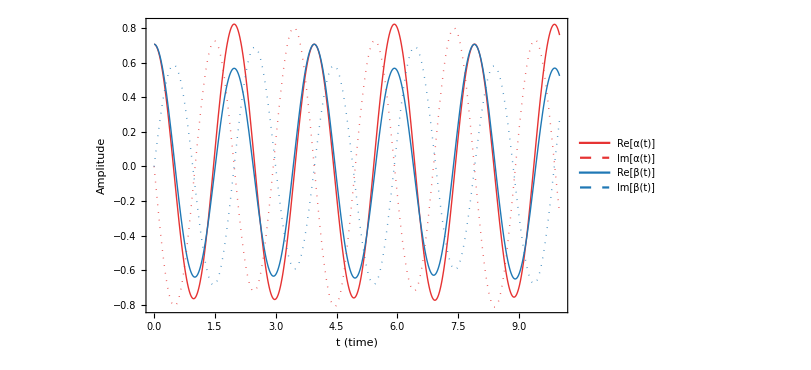

```mathematica
(* =====Batch export (runs only when $BatchMode=True)=====*)If[TrueQ@$BatchMode,Export[FileNameJoin[{figs,"wavefunction_ReImPlot.pdf"}],plt,"PDF"];
Export[FileNameJoin[{figs,"wavefunction_ReImPlot.png"}],plt,"PNG",ImageResolution->192,ImageSize->1200];
(*Optional numeric dump for downstream plots/tables*)ts=Table[{tt,Evaluate@Re[alpha[tt]/. sol],Evaluate@Im[alpha[tt]/. sol],Evaluate@Re[beta[tt]/. sol],Evaluate@Im[beta[tt]/. sol]},{tt,0,10,0.01}];
Export[FileNameJoin[{tabs,"wavefunction_ReIm_timeseries.csv"}],Prepend[ts,{"t","ReAlpha","ImAlpha","ReBeta","ImBeta"}],"CSV"];];
```